# Free energy relationships for nonadiabatic PCET

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/souda/Documents/Projects/Zach/inverted-region-model

```mathematica
Needs["MathPCET`"]
```

```mathematica
SetSystemOptions["CheckMachineUnderflow"->False];
```

## Parameters

## Marcus parameters

```mathematica
V=1;
λ=25;
T=298.15;
```

## Donor-acceptor harmonic potential

```mathematica
fR=0.051414;
MR=10;
R0=0.65 a2bohr;
ΩR=au2cm √(fR/(MR Dalton))
```

368.59

## Morse Parameters

Morse parameters for the reactant (1) and product (2) proton potentials

```mathematica
D1=100;(* kcal/mol *)
D2=100;(* kcal/mol *)
β1=1.96/a2bohr; (* Bohr^-1 *)
β2=2.16/a2bohr; (* Bohr^-1 *)
```

Harmonic Frequencies:

```mathematica
MorseOmega[DE_,β_,OptionsPattern[{M->MassH}]]:=Module[{μ,DEA},
	μ=OptionValue[M]*Dalton;
	DEA=DE*kcal2au;
	β*Sqrt[(2DEA)/μ]au2cm
];
```

```mathematica
Framed[
"Harmonic Frequencies\n"<>
"Reactant:"<>ToString[PaddedForm[MorseOmega[D1,β1],{8,2}]]<>" cm^-1\n"<>
"Product: "<>ToString[PaddedForm[MorseOmega[D2,β2],{8,2}]]<>" cm^-1",Background->Yellow
]
```

Harmonic Frequencies
Reactant:   2999.10 cm^-1
Product:    3305.13 cm^-1

```mathematica
μmaxH=MorseBound[β1,D1];
νmaxH=MorseBound[β2,D2];
Framed[
"Highest bound states for Hydrogen\n"<>
"Reactant: "<>ToString[μmaxH]<>"\n"<>
"Product:  "<>ToString[νmaxH],Background->Yellow
]
```

Highest bound states for Hydrogen
Reactant: 22
Product:  20

```mathematica
μmaxD=MorseBound[β1,D1,M->MassD];
νmaxD=MorseBound[β2,D2,M->MassD];
Framed[
"Highest bound states for Deuterium\n"<>
"Reactant: "<>ToString[μmaxD]<>"\n"<>
"Product:  "<>ToString[νmaxD],Background->Yellow
]
```

Highest bound states for Deuterium
Reactant: 32
Product:  29

```mathematica
Grid[{
{"","Number of bound states",SpanFromLeft},
{"","Hydrogen","Deuterium"},
{"Reactant",ToString[μmaxH],ToString[μmaxD]},
{"Product",ToString[νmaxH],ToString[νmaxD]}
},Frame->{All,{{{1,1},{1,2}}->False}}]
```

| Number of bound states | 
 | Hydrogen | Deuterium
Reactant | 22 | 32
Product | 20 | 29

Reactant and product Morse potentials:

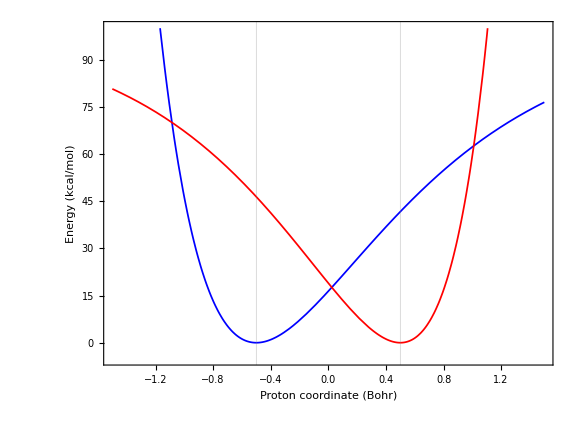

```mathematica
Plot[{MorsePotential[D1,β1,x+0.5],MorsePotentialInverted[D2,β2,x-0.5]},{x,-1.5,1.5},
Axes->False,Frame->True,
FrameLabel->{"Proton coordinate (Bohr)","Energy (kcal/mol)"},
PlotStyle->{{Blue,AbsoluteThickness[1.25]},{Red,AbsoluteThickness[1.25]}},
PlotRange->{-5,100},
BaseStyle->{FontSize->18,FontFamily->"Helvetica"},
FrameStyle->AbsoluteThickness[1.0],
ImageSize->Large,
GridLines->{{-0.5,0.5},None},
AspectRatio->0.75]
```

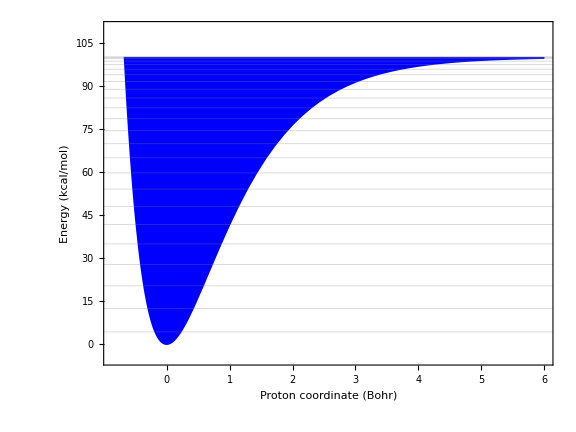

```mathematica
Plot[MorsePotential[D1,β1,x],{x,-1,6},
Axes->False,Frame->True,
FrameLabel->{"Proton coordinate (Bohr)","Energy (kcal/mol)"},
PlotStyle->{{Blue,AbsoluteThickness[1.25]},{Red,AbsoluteThickness[1.25]}},
PlotRange->{-5,D1+10},
BaseStyle->{FontSize->18,FontFamily->"Helvetica"},
FrameStyle->AbsoluteThickness[1.0],
Filling->{1->{D1,Blue}},
RegionFunction->Function[{x,y},y<D1],
ImageSize->Large,
GridLines->{None,Join[Table[{MorseEnergy[μ,β1,D1],{White,Thin}},{μ,0,μmax}],{{D1,{Red,Thin}}}]},
Method->{"GridLinesInFront"->True},
AspectRatio->0.75]
```

## DAD parameters

```mathematica
V=1;
λ=25;
T=298.15;
```

```mathematica
fR=0.051414;
MR=10;
R0=0.65 a2bohr;
ΩR=au2cm √(fR/(MR Dalton))
```

368.59

## Model based on Morse proton Potentials

## Vibrational Overlaps and Franck-Condon Factors

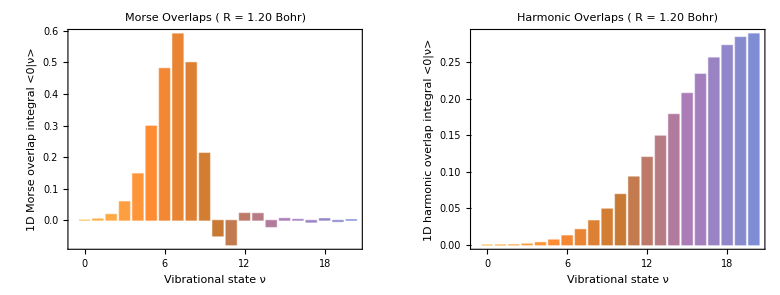

```mathematica
d=R0;
GraphicsRow[{
BarChart[
{Table[
MorseOverlap[D1,β1,D2,β2,0,i,d],
{i,0,νmax,1}]},
PlotRange->All,
PlotLabel->"Morse Overlaps ( R = "<>ToString[PaddedForm[d,{2,2}]]<>" Bohr)",
FrameLabel->{"Vibrational state ν","1D Morse overlap integral <0|ν>"},
Axes->False,Frame->True,
BaseStyle->{FontSize->12,FontFamily->"Helvetica",AbsoluteThickness[1.0]},
ImageSize->Medium,
FrameStyle->AbsoluteThickness[0.5],
AspectRatio->0.75,
ChartLabels->Flatten@Table[{i,""},{i,0,νmax,2}]],
BarChart[
{Table[
HarmonicOverlap[0,i,3000,3300,d],
{i,0,νmax,1}]},
PlotRange->All,
PlotLabel->"Harmonic Overlaps ( R = "<>ToString[PaddedForm[d,{2,2}]]<>" Bohr)",
FrameLabel->{"Vibrational state ν","1D harmonic overlap integral <0|ν>"},
Axes->False,Frame->True,
BaseStyle->{FontSize->12,FontFamily->"Helvetica",AbsoluteThickness[1.0]},
ImageSize->Medium,
FrameStyle->AbsoluteThickness[0.5],
AspectRatio->0.75,
ChartLabels->Flatten@Table[{i,""},{i,0,νmax,2}]]
}]
```

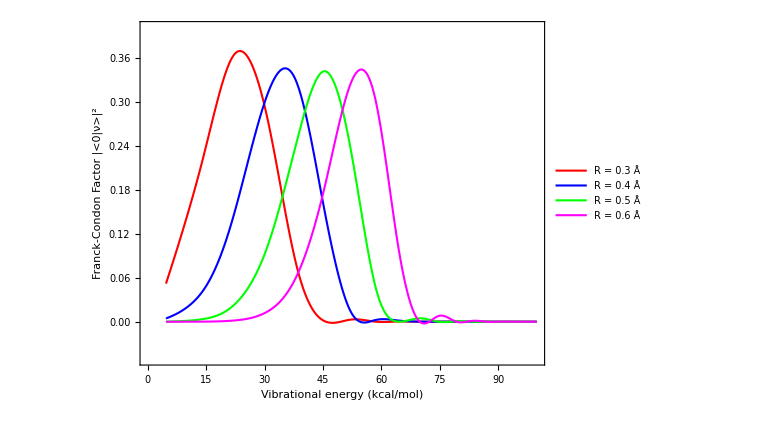

```mathematica
ListLinePlot[
{Table[{MorseEnergy[i,β2,D2],MorseOverlap[D1,β1,D2,β2,0,i,0.3a2bohr]^2},{i,0,νmax}],Table[{MorseEnergy[i,β2,D2],MorseOverlap[D1,β1,D2,β2,0,i,0.4a2bohr]^2},{i,0,νmax}],Table[{MorseEnergy[i,β2,D2],MorseOverlap[D1,β1,D2,β2,0,i,0.5a2bohr]^2},{i,0,νmax}],
Table[{MorseEnergy[i,β2,D2],MorseOverlap[D1,β1,D2,β2,0,i,0.6a2bohr]^2},{i,0,νmax}]},
PlotStyle->{Red,Blue,Green,Magenta},
PlotRange->{-0.05,0.4},
FrameLabel->{"Vibrational energy (kcal/mol)","Franck-Condon Factor |<0|ν>|^2"},
PlotLegends->Placed[{"R = 0.3 Å","R = 0.4 Å","R = 0.5 Å","R = 0.6 Å"},Right],
Axes->False,Frame->True,
BaseStyle->{FontSize->18,FontFamily->"Helvetica",AbsoluteThickness[1.5]},
FrameStyle->AbsoluteThickness[1.0],
AspectRatio->0.75,
InterpolationOrder->3,
Filling->None,
ImageSize->Large]
```

## Nonadiabatic Rates

### Checking integration over R

#### Averaged Franck-Condon Factors

```mathematica
MorseFranckCondonAveraged[mu_,nu_,DE1_,Beta1_,DE2_,Beta2_,d_,T_,MR_,FR_,OptionsPattern[{M->MassH,Overlap->"Numerical",Distribution->"Classical"}]]:=
Module[{m,sw,PR,s,distr,integrand,n,a,b,integral,error,regions,tol,absc,weights,errweights,c,r1,r2},
m=OptionValue[M];
distr=OptionValue[Distribution];
sw=OptionValue[Overlap];
PR[x_]:=Switch[distr,
"Classical",PClassical[T,d,MR,FR,x],
            "Quantal",  PQuantal[T,d,MR,FR,x],
            _,          PClassical[T,d,MR,FR,x]];
s[x_]:=Switch[sw,
	"Numerical",NMorseOverlap[DE1,Beta1,DE2,Beta2,mu,nu,x,M->m],
	"Analytical",MorseOverlap[DE1,Beta1,DE2,Beta2,mu,nu,x,M->m,Acc->50],
	"AnalyticalSym",MorseOverlapSym[DE1,Beta1,mu,nu,x,M->m],
	_,NMorseOverlap[DE1,Beta1,DE2,Beta2,mu,nu,x,M->m]];
integrand[x_]:=Abs[s[x]]^2*PR[x];
n=10;{absc,weights,errweights}=NIntegrate`GaussKronrodRuleData[n,50];tol=10^-8;
a=0;b=5;
{integral,error}=(b-a)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{a,b}],weights,errweights}];
regions={{{a,b},integral,Abs[error]}};
While[Abs[error]>= Abs[tol*integral],
(* splitting of the region with the largest error *)
{a,b}=regions⟦1,1⟧;c=(a+b)/2;
(* integration of the left region *)
{integral,error}=(c-a)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{a,c}],weights,errweights}];
r1={{a,c},integral,Abs[error]};
(* integration of the right region *)
{integral,error}=(b-c)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{c,b}],weights,errweights}];
r2={{c,b},integral,Abs[error]};
(* sort the regions: the largest error one is the first *)
regions=Join[{r1,r2},Rest[regions]];
regions=Sort[regions,#1⟦3⟧>#2⟦3⟧&];
(* global integral and error *)
{integral,error}=Total[Map[Rest[#1]&,regions]];
];
(*Print["Integration error: ",error];*)
integral
];
```

```mathematica
ΔG0=0;
kH0=TotalRateUKMorse[V,ΔG0,λ,MR,ΩR,D1,β1,D2,β2,R0,T,0,0,Overlap->"Numerical",Distribution->"Classical",M->MassH];
kD0=TotalRateUKMorse[V,ΔG0,λ,MR,ΩR,D1,β1,D2,β2,R0,T,0,0,Overlap->"Numerical",Distribution->"Classical",M->MassD];
KIE=KIEUKMorse[V,ΔG0,λ,MR,ΩR,D1,β1,D2,β2,R0,T,0,0,Overlap->"Numerical",Distribution->"Classical"];
Print["kH = ", kH0," s^-1"];
Print["kD = ",kD0," s^-1"];
Print["KIE = ",kH0/kD0];
Print["KIE = ",KIE];
```

kH = 16876.7 s^-1

kD = 510.514 s^-1

KIE = 33.0582

KIE = 33.0582

#### Averaging the rate constant itself

```mathematica
kHList=Table[
{
RR,
TotalRateRfixedMorse[V,0,λ,D1,β1,D2,β2,RR,T,0,0,Overlap->"Numerical",M->MassH]
},
{RR,0,5,0.01}
];
kDList=Table[
{
RR,
TotalRateRfixedMorse[V,0,λ,D1,β1,D2,β2,RR,T,0,0,Overlap->"Numerical",M->MassD]
},
{RR,0,5,0.01}
];
```

```mathematica
(*kHList//TableForm*)
```

```mathematica
kHR=Interpolation[kHList,Method->"Spline",InterpolationOrder->2]
kDR=Interpolation[kDList,Method->"Spline",InterpolationOrder->2]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
kH=NIntegrate[kHR[x]PClassical[T,R0,MR,ΩR,x],{x,0,5}]
kD=NIntegrate[kDR[x]PClassical[T,R0,MR,ΩR,x],{x,0,5}]
kH/kD
```

16876.6

510.51

33.0583

### Convergence of the rate constants at various ΔG:

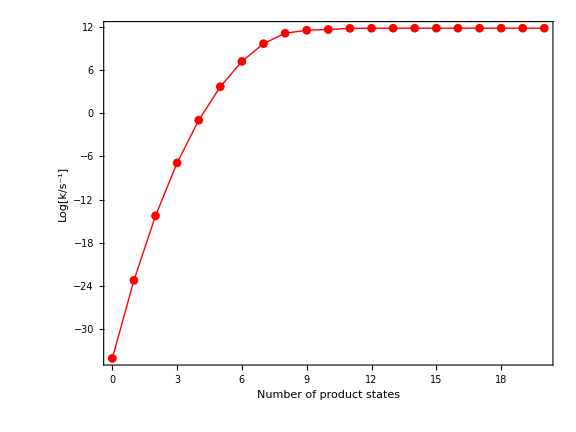

```mathematica
ΔG0=-100;
ListLinePlot[Table[{ν,Log[10,TotalRateUKMorse[V,ΔG0,λ,MR,ΩR,D1,β1,D2,β2,R0,T,3,ν,Overlap->"Numerical",Distribution->"Classical"]]},{ν,0,νmax}],Axes->False,Frame->True,PlotMarkers->Automatic,PlotRange->All,PlotStyle->{{Red,AbsoluteThickness[1.0]}},FrameStyle->AbsoluteThickness[1.0],BaseStyle->{FontSize->18,FontFamily->"Helvetica"},FrameLabel->{"Number of product states","Log[k/s^-1]"},ImageSize->Large,AspectRatio->0.75]
```

### Energy Gap Law

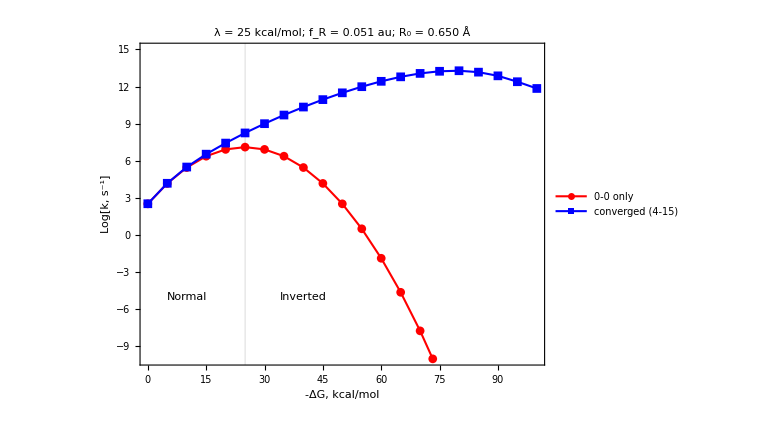

```mathematica
Framed@ListLinePlot[{
Table[{x,Log[10,TotalRateUKMorse[V,-x,λ,MR,ΩR,D1,β1,D2,β2,R0,T,0,0,Overlap->"Numerical",Distribution->"Classical"]]},{x,0,100,5}],
Table[{x,Log[10,TotalRateUKMorse[V,-x,λ,MR,ΩR,D1,β1,D2,β2,R0,T,4,12,Overlap->"Numerical",Distribution->"Classical"]]},{x,0,100,5}]},
Axes->False,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},
PlotRange->{-10,15},
PlotStyle->{{Red,AbsoluteThickness[1.5]},{Blue,AbsoluteThickness[1.5]}},
PlotLabel->"λ = "<>ToString[λ]<>" kcal/mol; f_R = "<>ToString@PaddedForm[fR,{4,3}]<>" au; R_0 = "<>ToString@PaddedForm[R0 bohr2a,{4,3}]<>" Å",
FrameStyle->AbsoluteThickness[1.0],
BaseStyle->{FontSize->18,FontFamily->"Helvetica"},
PlotMarkers->Automatic,
FrameLabel->{"-ΔG, kcal/mol","Log[k, s^-1]"},
PlotLegends->Placed[{"0-0 only","converged (4-15)"},Right],
ImageSize->Large,AspectRatio->0.75,GridLines->{{λ},None},
Epilog->{Inset["Inverted",{40,-5}],Inset["Normal",{10,-5}]}]
```

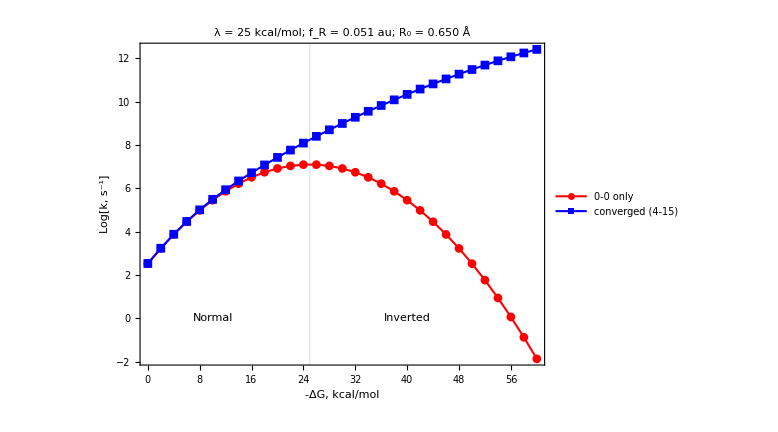

```mathematica
Framed@ListLinePlot[{
Table[{x,Log[10,TotalRateUKMorse[V,-x,λ,MR,ΩR,D1,β1,D2,β2,R0,T,0,0,Overlap->"Numerical",Distribution->"Classical"]]},{x,0,60,2}],
Table[{x,Log[10,TotalRateUKMorse[V,-x,λ,MR,ΩR,D1,β1,D2,β2,R0,T,4,15,Overlap->"Numerical",Distribution->"Classical"]]},{x,0,60,2}]},
Axes->False,Frame->True,
FrameTicks->{{Automatic,None},{Automatic,None}},
PlotStyle->{{Red,AbsoluteThickness[1.5]},{Blue,AbsoluteThickness[1.5]}},
PlotLabel->"λ = "<>ToString[λ]<>" kcal/mol; f_R = "<>ToString@PaddedForm[fR,{4,3}]<>" au; R_0 = "<>ToString@PaddedForm[R0 bohr2a,{4,3}]<>" Å",
FrameStyle->AbsoluteThickness[1.0],
BaseStyle->{FontSize->18,FontFamily->"Helvetica"},
PlotLegends->Placed[{"0-0 only","converged (4-15)"},Right],
PlotMarkers->Automatic,
FrameLabel->{"-ΔG, kcal/mol","Log[k, s^-1]"},
ImageSize->Large,AspectRatio->0.75,GridLines->{{λ},None},
Epilog->{Inset["Inverted",{40,0}],Inset["Normal",{10,0}]}]
```

```mathematica
MorseFranckCondonAveraged[0,12,D1,β1,D2,β2,1.5,T,MR,ΩR,Overlap->"Analytical",Distribution->"Classical"]
```

0.0141433

### KIE

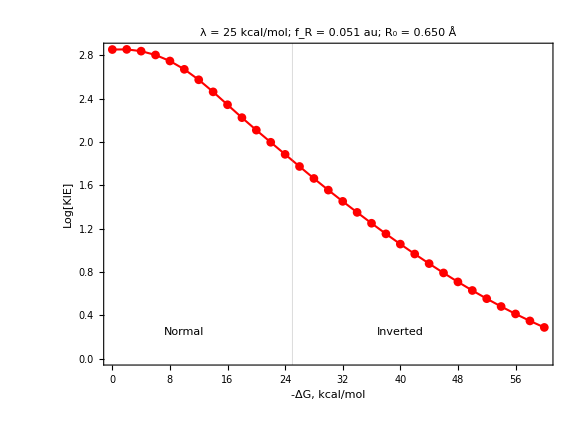

```mathematica
Framed@ListLinePlot[{
Table[{x,Log10@KIEUKMorse[V,-x,λ,MR,ΩR,D1,β1,D2,β2,R0,T,4,15,Overlap->"Numerical",Distribution->"Classical"]},{x,0,60,2}]},
Axes->False,Frame->True,
FrameTicks->{{Automatic,None},{Automatic,None}},
PlotStyle->{{Red,AbsoluteThickness[1.5]},{Blue,AbsoluteThickness[1.5]}},
PlotLabel->"λ = "<>ToString[λ]<>" kcal/mol; f_R = "<>ToString@PaddedForm[fR,{4,3}]<>" au; R_0 = "<>ToString@PaddedForm[R0 bohr2a,{4,3}]<>" Å",
FrameStyle->AbsoluteThickness[1.0],
BaseStyle->{FontSize->18,FontFamily->"Helvetica"},
PlotMarkers->Automatic,
ScalingFunctions->{None,None},
FrameLabel->{"-ΔG, kcal/mol","Log[KIE]"},
ImageSize->Large,AspectRatio->0.75,GridLines->{{λ},None},
Epilog->{Inset["Inverted",{40,0.25}],Inset["Normal",{10,0.25}]}]
```

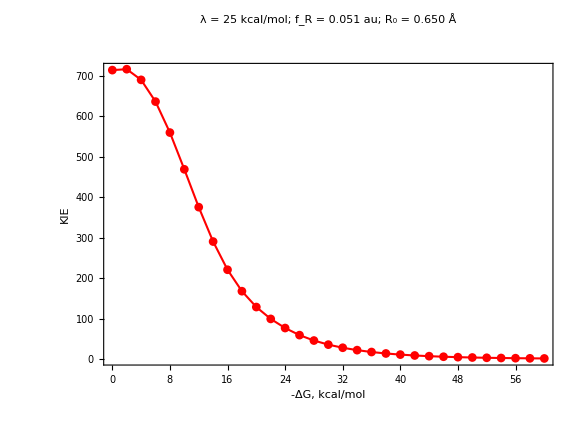

```mathematica
Framed@ListLinePlot[{
Table[{x,KIEUKMorse[V,-x,λ,MR,ΩR,D1,β1,D2,β2,R0,T,4,15,Overlap->"Numerical",Distribution->"Classical"]},{x,0,60,2}]},
Axes->False,Frame->True,
FrameTicks->{{Automatic,None},{Automatic,None}},
PlotStyle->{{Red,AbsoluteThickness[1.5]},{Blue,AbsoluteThickness[1.5]}},
PlotLabel->"λ = "<>ToString[λ]<>" kcal/mol; f_R = "<>ToString@PaddedForm[fR,{4,3}]<>" au; R_0 = "<>ToString@PaddedForm[R0 bohr2a,{4,3}]<>" Å",
FrameStyle->AbsoluteThickness[1.0],
BaseStyle->{FontSize->18,FontFamily->"Helvetica"},
PlotMarkers->Automatic,
FrameLabel->{"-ΔG, kcal/mol","KIE"},
ImageSize->Large,AspectRatio->0.75,GridLines->{{-λ},None},
Epilog->{Inset["Inverted",{40,800}],Inset["Normal",{10,800}]}]
```

## Model Based on Double-Well Proton Potentials

## Proton Potentials from the 2-State PT Model (1a/1b)

```mathematica
Ua[DE_,Beta_,x_]:=MorsePotential[DE,Beta,x];
Ub[DE_,Beta_,x_]:=MorsePotentialInverted[DE,Beta,x];
```

The diabatic potentials used in this model must always cross at least at one point

```mathematica
U[DE1_,Beta1_,DE2_,Beta2_,VPT_,Δ_,R_,x_]:=Module[{h11,h22,ua,u,xp,nX,xpl,xp1,xpr,swf0,swf1,swf2},
xp=NSolve[Ua[DE1,Beta1,y+R/2]==Ub[DE2,Beta2,y-R/2]+Δ,y,Reals];
nX=Length[xp];
If[nX==0,
Print["No crossings between the diabatic potentials found: something is wrong!"];
Return[Null]
];
If[nX>1,
xpl=xp⟦1,1,2⟧;
xpr=xp⟦nX,1,2⟧,
xp1=xp⟦1,1,2⟧;
If[xp1<0,xpl=xp1;xpr=R/2,xpl=-R/2;xpr=xp1]
];
swf0[y_]:=1/2(1-Tanh[5y]);
swf1[y_]:=1/2(1-Tanh[5(y-xpl)]);
swf2[y_]:=1/2(1+Tanh[5(y-xpr)]);
h11=Ua[DE1,Beta1,x+R/2];
h22=Ub[DE2,Beta2,x-R/2]+Δ;
ua=1/2(h11+h22)-1/2 √((h11-h22)^2+4 VPT^2);
swf0[x](swf1[x]h11+(1-swf1[x])ua)+(1-swf0[x])((1-swf2[x])ua+swf2[x]h22)
];
```

```mathematica
R0
```

1.22832

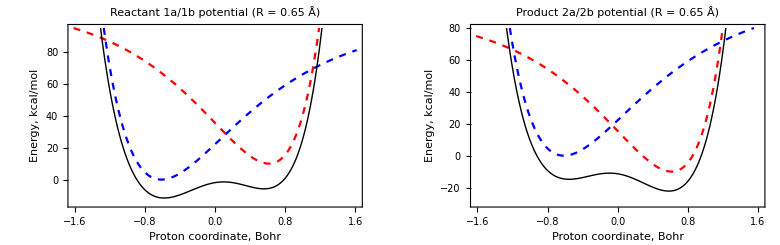

```mathematica
RR=R0;
Δ=10;
VPT=30;
GraphicsRow[{
Plot[
{Ua[D1,β1,x+RR/2],
Ub[D2,β2,x-RR/2]+Δ,
U[D1,β1,D2,β2,VPT,Δ,RR,x]},{x,-RR/2-1,RR/2+1},
Axes->False,Frame->True,
PlotRange->{-15,95},
PlotLabel->"Reactant 1a/1b potential (R = "<>ToString[RR bohr2a]<>" Å)" ,
FrameLabel->{"Proton coordinate, Bohr","Energy, kcal/mol"},
PlotStyle->{{Blue,Dashed},{Red,Dashed},{Black,Thick}},
ImageSize->Medium
],
Plot[
{Ua[D1,β1,x+RR/2],
Ub[D2,β2,x-RR/2]-Δ,
U[D1,β1,D2,β2,VPT,-Δ,RR,x]},{x,-RR/2-1,RR/2+1},
Axes->False,Frame->True,
PlotRange->{-30,80},
PlotLabel->"Product 2a/2b potential (R = "<>ToString[RR bohr2a]<>" Å)" ,
FrameLabel->{"Proton coordinate, Bohr","Energy, kcal/mol"},
PlotStyle->{{Blue,Dashed},{Red,Dashed},{Black,Thick}},
ImageSize->Medium
]
}]
```

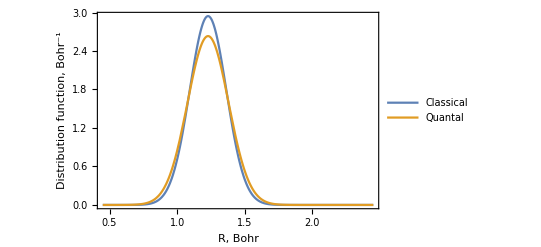

```mathematica
Plot[{PClassical[T,R0,MR,ΩR,x],PQuantal[T,R0,MR,ΩR,x]},{x,0.45,2.45},
PlotRange->All,Axes->False,Frame->True,
FrameLabel->{"R, Bohr","Distribution function, Bohr^-1"},
PlotLegends->Placed[{"Classical","Quantal"},{0.75,0.5}]]
```

## Grid of Donor-Acceptor Distances

```mathematica
Rlist=Table[x,{x,0.5,2.0,0.01}]
```

{0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.,1.01,1.02,1.03,1.04,1.05,1.06,1.07,1.08,1.09,1.1,1.11,1.12,1.13,1.14,1.15,1.16,1.17,1.18,1.19,1.2,1.21,1.22,1.23,1.24,1.25,1.26,1.27,1.28,1.29,1.3,1.31,1.32,1.33,1.34,1.35,1.36,1.37,1.38,1.39,1.4,1.41,1.42,1.43,1.44,1.45,1.46,1.47,1.48,1.49,1.5,1.51,1.52,1.53,1.54,1.55,1.56,1.57,1.58,1.59,1.6,1.61,1.62,1.63,1.64,1.65,1.66,1.67,1.68,1.69,1.7,1.71,1.72,1.73,1.74,1.75,1.76,1.77,1.78,1.79,1.8,1.81,1.82,1.83,1.84,1.85,1.86,1.87,1.88,1.89,1.9,1.91,1.92,1.93,1.94,1.95,1.96,1.97,1.98,1.99,2.}

```mathematica
NR=Length[Rlist]
```

151

```mathematica
R0
```

1.22832

```mathematica
iR0=Flatten[Position[Rlist,1.23]]⟦1⟧
```

74

## Create External Files with Proton Potentials

```mathematica
Δ=10;
VPT=30;
Monitor[
Block[{i,Δx,RR,nG,fileName,potentialList},
nG=256;
Δx=1.5;
DeleteFile[FileNames["protonPotentialsR*.dat"]];
For[i=1,i<NR+1,i++,
RR=Rlist⟦i⟧;
fileName="protonPotentialsR"<>ToString[PaddedForm[RR,{3,3},NumberPadding->{"","0"},NumberPoint->""]]<>".dat";
potentialList=Table[{x bohr2a,U[D1,β1,D2,β2,VPT,Δ,RR,x]kcal2au,U[D1,β1,D2,β2,VPT,-Δ,RR,x]kcal2au},{x,-RR/2-Δx,RR/2+Δx,(RR+2Δx)/(nG-1)}];
Export[fileName,potentialList,"Data"];
]
],
Panel@Grid[
{
{"R gridpoint:",ProgressIndicator[i,{1,NR}],PaddedForm[Rlist⟦i⟧,{3,2}],"Bohr"}
},
Alignment->{{Right,Left,Center,Right,Left}},Spacings->1]
];
```

## Solving Schrödinger Equations for all Proton Potentials

```mathematica
Monitor[
Block[{nG,i,RR,fileName,potentialList},
nG=1024;
FGHlistH={};
FGHlistD={};
For[i=1,i<NR+1,i++,
RR=Rlist⟦i⟧;
fileName="protonPotentialsR"<>ToString[PaddedForm[RR,{3,3},NumberPadding->{"","0"},NumberPoint->""]]<>".dat";
AppendTo[FGHlistH,FGHWavefunctions[fileName,nG,30,M->MassH]];
AppendTo[FGHlistD,FGHWavefunctions[fileName,nG,30,M->MassD]]
]
],
Panel@Grid[
{
{"R =",PaddedForm[Rlist⟦i⟧,{3,2}],"Bohr",ProgressIndicator[i,{1,NR}],i}
},
Alignment->{{Right,Left,Center,Right,Left}},Spacings->1]
];
```

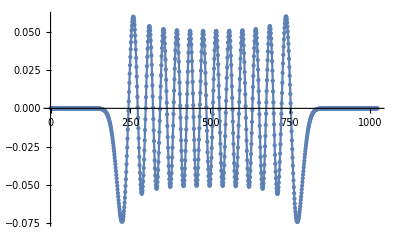

```mathematica
ListLinePlot[FGHlistD⟦2⟧⟦1,3,25⟧,PlotRange->All,Mesh->Full,MeshStyle->PointSize[Medium]]
```

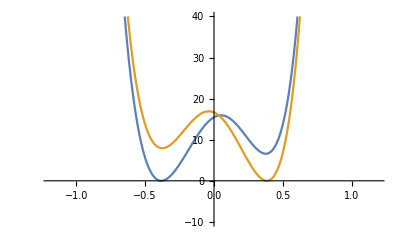

```mathematica
ListLinePlot[{FGHlistD⟦100⟧⟦1,2⟧,FGHlistD⟦100⟧⟦2,2⟧},PlotRange->{-10,40},Mesh->None]
```

```mathematica
Length[FGHlistH⟦iR0⟧⟦3⟧⟦1,All⟧]
```

30

```mathematica
FrameLabel->{"Vibrational state ν","FGH overlap integral <0|ν>"},
Axes->False,Frame->True,
```

```mathematica
PairedBarChart[
Abs@FGHlistH⟦iR0⟧⟦3⟧⟦1,All⟧,
Abs@FGHlistD⟦iR0⟧⟦3⟧⟦1,All⟧,
ChartStyle->{{Red,Blue},None,None},
ChartLegends->Placed[{{"Hydrogen", "Deuterium"}, None, None},Bottom],
PlotRange->All,
PlotLabel->"FGH Overlap Integrals (R ="<>ToString[PaddedForm[R0,{4,3}]]<>" Bohr)",
BaseStyle->{FontSize->14,FontFamily->"Helvetica",AbsoluteThickness[1.0]},
ImageSize->Large,
FrameStyle->AbsoluteThickness[0.5],
AspectRatio->0.75,
ChartLabels->Flatten@Table[{i,""},{i,0,29,2}]]
```

-Graphics-

## Calculate Rates and KIEs

```mathematica
rateRH[V_,ΔG_,λ_,T_,μmax_,νmax_]:=Table[TotalRateRfixedFGH[FGHlistH⟦i⟧,V,ΔG,λ,T,μmax,νmax],{i,1,NR}];
rateRD[V_,ΔG_,λ_,T_,μmax_,νmax_]:=Table[TotalRateRfixedFGH[FGHlistD⟦i⟧,V,ΔG,λ,T,μmax,νmax],{i,1,NR}];
```

```mathematica
rateH[V_,ΔG_,λ_,T_,R0_,MR_,ΩR_,μmax_,νmax_]:=Module[{rateR,PR,h,fa,fb},
rateR=rateRH[V,ΔG,λ,T,μmax,νmax];
PR=Table[PClassical[T,R0,MR,ΩR,Rlist⟦i⟧],{i,1,NR}];
f=rateR*PR;
fa=f⟦1⟧;
fb=f⟦NR⟧;
h=Rlist⟦2⟧-Rlist⟦1⟧;
1/2 h fa+h Sum[f⟦i⟧,{i,2,NR-1}]+1/2 h fb
];
rateD[V_,ΔG_,λ_,T_,R0_,MR_,ΩR_,μmax_,νmax_]:=Module[{rateR,PR,h,fa,fb},
rateR=rateRD[V,ΔG,λ,T,μmax,νmax];
PR=Table[PClassical[T,R0,MR,ΩR,Rlist⟦i⟧],{i,1,NR}];
f=rateR*PR;
fa=f⟦1⟧;
fb=f⟦NR⟧;
h=Rlist⟦2⟧-Rlist⟦1⟧;
1/2 h fa+h Sum[f⟦i⟧,{i,2,NR-1}]+1/2 h fb
];
```

```mathematica
KIE[V_,ΔG_,λ_,T_,R0_,MR_,ΩR_,μmax_,νmax_]:=rateH[V,ΔG,λ,T,R0,MR,ΩR,μmax,νmax]/rateD[V,ΔG,λ,T,R0,MR,ΩR,μmax,νmax];
```

```mathematica
ratesG0=rateRH[V,-100,λ,T,3,25];
```

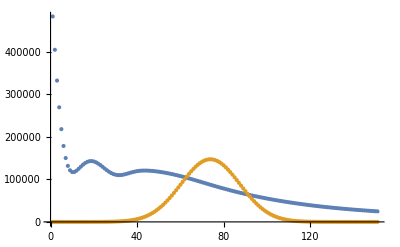

```mathematica
ListPlot[{ratesG0,Table[5×10^4 PClassical[T,R0,MR,ΩR,Rlist⟦i⟧],{i,1,NR}]},PlotRange->All]
```

Weighted rates

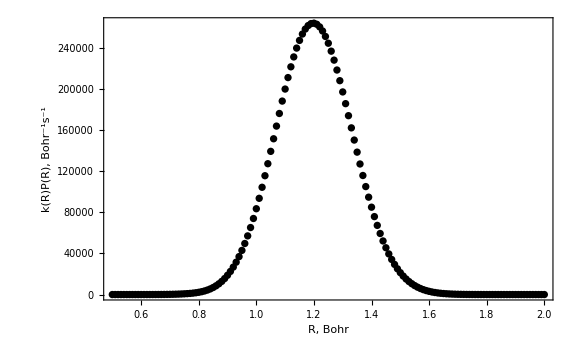

```mathematica
ListPlot[{Table[{Rlist⟦i⟧,PClassical[T,R0,MR,ΩR,Rlist⟦i⟧]ratesG0⟦i⟧},{i,1,NR}]},
PlotRange->All,
Axes->False,Frame->True,
BaseStyle->{FontSize->16,FontFamily->"Helvetica",Black},
FrameLabel->{"R, Bohr","k(R)P(R), Bohr^-1s^-1"},
LabelStyle->Black,
ImageSize->Large
]
```

## Plots

```mathematica
TotalRateRfixedFGH[FGHlistH⟦200⟧,V,-100,λ,T,2,25]
```

14553.

```mathematica
rateH[V,-100,λ,T,R0,MR,ΩR,4,25]
rateD[V,-100,λ,T,R0,MR,ΩR,4,25]
KIE[V,-100,λ,T,R0,MR,ΩR,4,25]
```

87508.2

225.233

388.523

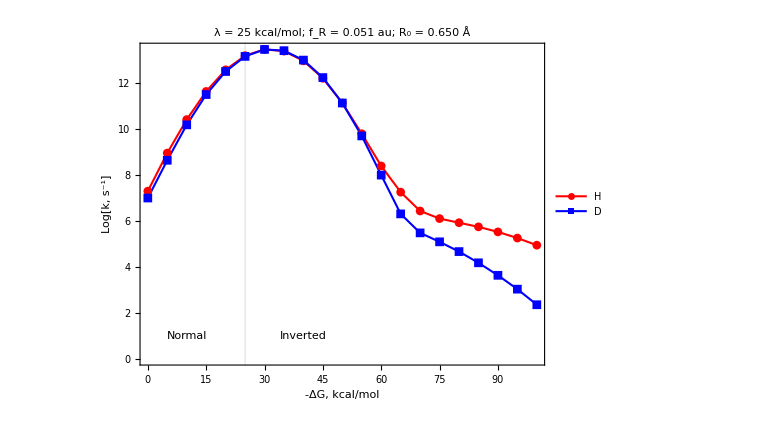

```mathematica
ListLinePlot[
{
Table[{x,Log[10,rateH[V,-x,λ,T,R0,MR,ΩR,3,25]]},{x,0,100,5}],
Table[{x,Log[10,rateD[V,-x,λ,T,R0,MR,ΩR,4,25]]},{x,0,100,5}]
},
Axes->False,Frame->True,
FrameTicks->{{Automatic,None},{Automatic,None}},
PlotStyle->{{Red,AbsoluteThickness[1.5]},{Blue,AbsoluteThickness[1.5]}},
PlotLabel->"λ = "<>ToString[λ]<>" kcal/mol; f_R ="<>ToString@PaddedForm[MR Dalton (ΩR cm2au)^2,{4,3}]<>" au; R_0 = "<>ToString@PaddedForm[R0 bohr2a,{4,3}]<>" Å",
FrameStyle->AbsoluteThickness[1.0],
BaseStyle->{FontSize->18,FontFamily->"Helvetica"},
PlotLegends->Placed[{"H","D"},Right],
PlotMarkers->Automatic,
FrameLabel->{"-ΔG, kcal/mol","Log[k, s^-1]"},LabelStyle->Black,
ImageSize->Large,AspectRatio->0.75,GridLines->{{λ},None},
Epilog->{Inset["Inverted",{40,1}],Inset["Normal",{10,1}]}]
```

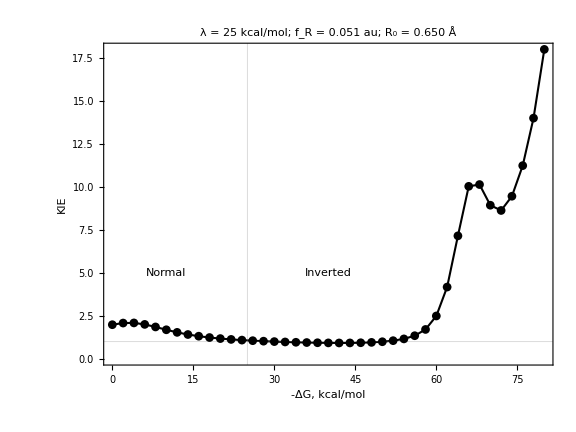

```mathematica
ListLinePlot[
{
Table[{x,KIE[V,-x,λ,T,R0,MR,ΩR,3,25]},{x,0,80,2}]
},
Axes->False,Frame->True,
FrameTicks->{{Automatic,None},{Automatic,None}},
PlotStyle->{{Black,AbsoluteThickness[1.5]}},
PlotLabel->"λ = "<>ToString[λ]<>" kcal/mol; f_R ="<>ToString@PaddedForm[MR Dalton (ΩR cm2au)^2,{4,3}]<>" au; R_0 = "<>ToString@PaddedForm[R0 bohr2a,{4,3}]<>" Å",
FrameStyle->AbsoluteThickness[1.0],
BaseStyle->{FontSize->18,FontFamily->"Helvetica"},
PlotMarkers->Automatic,
FrameLabel->{"-ΔG, kcal/mol","KIE"},LabelStyle->Black,
ImageSize->Large,AspectRatio->0.75,GridLines->{{λ},{1}},
Epilog->{Inset["Inverted",{40,5}],Inset["Normal",{10,5}]}]
```

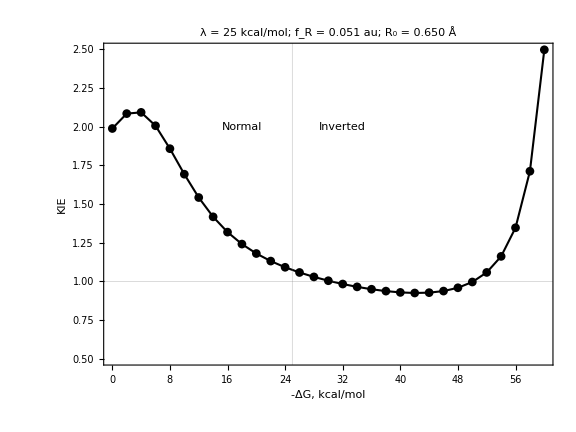

```mathematica
ListLinePlot[
{
Table[{x,KIE[V,-x,λ,T,R0,MR,ΩR,3,25]},{x,0,60,2}]
},
Axes->False,Frame->True,
PlotRange->{0.5,2.5},
FrameTicks->{{Automatic,None},{Automatic,None}},
PlotStyle->{{Black,AbsoluteThickness[1.5]}},
PlotLabel->"λ = "<>ToString[λ]<>" kcal/mol; f_R ="<>ToString@PaddedForm[MR Dalton (ΩR cm2au)^2,{4,3}]<>" au; R_0 = "<>ToString@PaddedForm[R0 bohr2a,{4,3}]<>" Å",
FrameStyle->AbsoluteThickness[1.0],
BaseStyle->{FontSize->18,FontFamily->"Helvetica"},
PlotMarkers->Automatic,
FrameLabel->{"-ΔG, kcal/mol","KIE"},LabelStyle->Black,
ImageSize->Large,AspectRatio->0.75,GridLines->{{λ},{1}},
Epilog->{Inset["Inverted",{32,2}],Inset["Normal",{18,2}]}]
```